#### Kac Determinant

```mathematica
h0 = 1/24(c-1);
αplus =(Sqrt[1-c]+Sqrt[25-c])/Sqrt[24];
αminus =(Sqrt[1-c]-Sqrt[25-c])/Sqrt[24];
hc[r_,s_]:=h0+1/4(r αplus + s αminus)^2;
```

```mathematica
m[r_,s_,l_] := PartitionsP[l-r s]-PartitionsP[l-r(s+1)];
a[l_]:=Product[ ((2 r)^s Factorial[s])^m[r,s,l],{r,1,l},{s,1,Quotient[l,r]}]
```

```mathematica
DetM[l_]:=a[l]Product[ (h-hc[r,s])^PartitionsP[l-r s],{r,1,l},{s,1,Quotient[l,r]}]
```

```mathematica
Simplify[DetM[2],c>0&&h>0]
```

2 h (c+2 c h+2 h (-5+8 h))

```mathematica
Simplify[DetM[3],c>0&&h>0]
```

48 h^2 (c^2 (1+3 h+2 h^2)+c (2-13 h-5 h^2+22 h^3)+2 h (-10+51 h-71 h^2+24 h^3))

```mathematica
Subscript[h, 2,1] = Simplify[hc[2,1],c>0&&h>0]
```

1/16 (5+√(1-c) √(25-c)-c)

```mathematica
Subscript[h, 1,2] = Simplify[hc[1,2],c>0&&h>0]
```

1/16 (5-√(1-c) √(25-c)-c)

```mathematica
Subscript[h, 3,1] = Simplify[hc[3,1],c>0&&h>0]
```

1/6 (7+√(1-c) √(25-c)-c)

```mathematica
Subscript[h, 1,3] =Simplify[hc[1,3],c>0&&h>0]
```

1/6 (7-√(1-c) √(25-c)-c)

```mathematica
Subscript[h, 4,1]=Simplify[hc[4,1],c>0&&h>0]
```

1/16 (41+5 √(1-c) √(25-c)-5 c)

```mathematica
Subscript[h, 1,4]=Simplify[hc[1,4],c>0&&h>0]
```

1/16 (41-5 √(1-c) √(25-c)-5 c)

```mathematica
Subscript[h, 2,2]=Simplify[hc[2,2],c>0&&h>0]
```

(1-c)/8

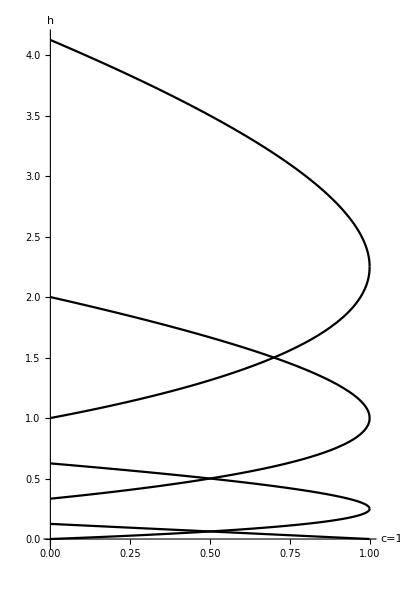

```mathematica
Plot[{Subscript[h, 1,2],Subscript[h, 2,1],Subscript[h, 1,3],Subscript[h, 3,1],Subscript[h, 4,1],Subscript[h, 1,4],Subscript[h, 2,2]},{c,0,1},AspectRatio->1.5,AxesStyle->Black,AxesLabel->{HoldForm[c=1],HoldForm[h]},PlotLabel->None,LabelStyle->{GrayLevel[0]},Ticks->None,PlotStyle->Black]
```

```mathematica
Export["Kac-Determinant.pdf",Out[102]]
```

Kac-Determinant.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Kac-Determinant.pdf"]]]
```

```mathematica
SystemOpen["Kac-Determinant.pdf"]
```

```mathematica
Subscript[h, 3,4] = Simplify[hc[3,4],c>0&&h>0]
```

1/48 (35-7 √(1-c) √(25-c)-23 c)

```mathematica
Subscript[h, 2,3] = Simplify[hc[2,3],c>0&&h>0]
```

1/48 (23-5 √(1-c) √(25-c)-11 c)

```mathematica
Subscript[h, 1,2] = Simplify[hc[1,2],c>0&&h>0]
```

1/16 (5-√(1-c) √(25-c)-c)

```mathematica
Subscript[h, 2,4] = Simplify[hc[2,4],c>0&&h>0]
```

1/8 (11-2 √(1-c) √(25-c)-3 c)

```mathematica
Subscript[h, 1,3] = Simplify[hc[1,3],c>0&&h>0]
```

1/6 (7-√(1-c) √(25-c)-c)

```mathematica
Subscript[h, 2,1] = Simplify[hc[2,1],c>0&&h>0]
```

1/16 (5+√(1-c) √(25-c)-c)

```mathematica
Subscript[h, 3,2] = Simplify[hc[3,2],c>0&&h>0]
```

1/48 (23+5 √(1-c) √(25-c)-11 c)

```mathematica
Subscript[h, 1,4] = Simplify[hc[1,4],c>0&&h>0]
```

1/16 (41-5 √(1-c) √(25-c)-5 c)

```mathematica
Subscript[h, 4,3] = Simplify[hc[4,3],c>0&&h>0]
```

1/48 (35+7 √(1-c) √(25-c)-23 c)

```mathematica
Subscript[h, 3,1] = Simplify[hc[3,1],c>0&&h>0]
```

1/6 (7+√(1-c) √(25-c)-c)

```mathematica
Subscript[h, 4,2] = Simplify[hc[4,2],c>0&&h>0]
```

1/8 (11+2 √(1-c) √(25-c)-3 c)

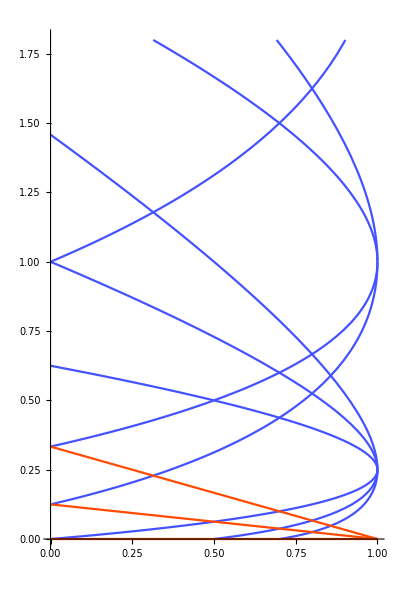

```mathematica
Show[Plot[{Subscript[h, 3,4],Subscript[h, 2,3],Subscript[h, 1,2] ,Subscript[h, 2,4],Subscript[h, 1,3],Subscript[h, 2,1],Subscript[h, 3,2],Subscript[h, 1,4] ,Subscript[h, 4,3] ,Subscript[h, 3,1],Subscript[h, 4,2] },{c,0,1},PlotRange->{{0,1},{0,1.8}},AspectRatio->1.5,PlotLabel->None,LabelStyle->{GrayLevel[0]},Ticks->None,PlotStyle->RGBColor[0.27,0.32,1.]],Plot[{Subscript[h, 1,1],Subscript[h, 2,2],Subscript[h, 3,3]},{c,0,1},PlotStyle->RGBColor[1.,0.29,0.]]]
```

```mathematica
Show[%48,ImageSize->Full]
```

-Graphics-

```mathematica
Export["E:\\CFT-lecture-notes\\picture\\Kac-Determinant.pdf",%52,"PDF"]
```

E:\CFT-lecture-notes\picture\Kac-Determinant.pdf

```mathematica
Export["Kac-Determinant.pdf",Out[48]]
```

Kac-Determinant.pdf

```mathematica
SystemOpen["Kac-Determinant.pdf"]
```

```mathematica
Show[%48,AxesStyle->Black]
```

-Graphics-

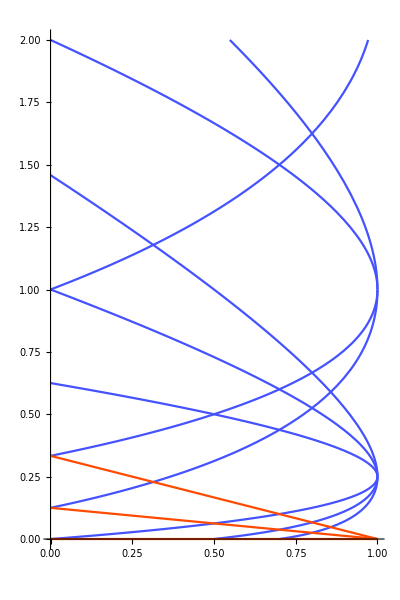

```mathematica
Show[%46,AxesStyle->Black]
```

```mathematica
Subscript[h, 1,1] = Simplify[hc[1,1],c>0&&h>0]
```

0

```mathematica
Subscript[h, 2,2] = Simplify[hc[2,2],c>0&&h>0]
```

(1-c)/8

```mathematica
Subscript[h, 3,3] = Simplify[hc[3,3],c>0&&h>0]
```

(1-c)/3